```mathematica
Clear["Global`*"]
notation ={wa->Subscript[ω, a],wo->Subscript[ω, 0],wp->Subscript[ω, p],deltaA->Subscript[Δ, a],deltaO->Subscript[Δ, 0], cb ->Subscript[c, b] ,ca ->Subscript[c, a],
uab->Subscript[μ, ab],uba->Subscript[μ, ba],  eps ->ℰ, cbnp1 -> Subscript[c,b,n+1], cn0 -> Subscript[c, n0]};
```

g2 plot from theory paper (plot repeated in matlab)

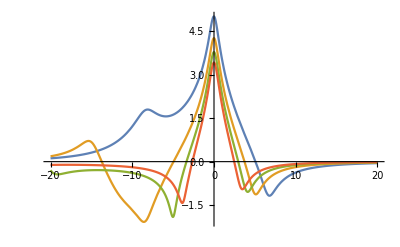

```mathematica
k = 1;
gamma=k;
eps = 0.01;

dap = da - I*k/2;
dop = do -I*gamma/2;
C2g = (eps^2* ((dap + dop)*dop + g^2))/(Sqrt[2](dap*dop-g^2)*((dap+dop)*dap-g^2));
C1g = (eps*dop)/(g^2-dap*dop);
g2 = (2*Abs[C2g]^2)/Abs[C1g]^4;
lg2 = Log10[g2];
strongc = lg2 /.g->10;
Plot[{strongc /.da->15,strongc /.da->20,strongc /.da->25,strongc /.da->30}, {do,-20,20},PlotRange->All]
```

Section A
Energy eigenvalues for strong coupling g>>(Κ,γ)

```mathematica
H = {{n*wa,g*Sqrt[n]},{g*Sqrt[n],wo+(n-1)*wa}};
MatrixForm[H] /. notation
En=Eigenvalues[H]//Simplify;
En /. notation
Eminus = En[[1]];
Eplus = En[[2]];
Epm = 1/2 ((-1+2 n) wa + PlusMinus[√(4 g^2 n+(wa-wo)^2)]+wo) ;
```

(n ω_a | g √n
g √n | ω_0+(-1+n) ω_a)

{1/2 (ω_0+(-1+2 n) ω_a-√(4 g^2 n+(-ω_0+ω_a)^2)),1/2 (ω_0+(-1+2 n) ω_a+√(4 g^2 n+(-ω_0+ω_a)^2))}

Case for same detuning Δ_0=Δ_a, ω_0=ω_a
The eigenvalues simplify to:

```mathematica
Epmsame = Epm /. wo -> wa
```

1/2 (wa+(-1+2 n) wa+±(2 √(g^2 n)))

First consider n=1.
For resonance, the photon energy must be equal to the excited state transition energy, ω_p=E_(1,±).

```mathematica
Clear[wp]
eq = Thread[wp == Epmsame] /. n->1;
eq  //Simplify
```

2 wa+±(2 √(g^2))==2 wp

Subtracting 2 ω_p from both sides in order to write the equation in terms of detuning, (and dividing both sides by 2)

```mathematica
eq = Thread[ wa+±(√(g^2))-wp==0] /. wa -> deltaA + wp //Simplify ;
eq /.notation
```

±√(g^2)+Δ_a==0

Finally, solve for detuning needed for n=1 resonance:

```mathematica
Solve[eq, deltaA]//FullSimplify
```

{{deltaA→-±√(g^2)}}

Thus for equal detuning, the resonance condition is that Δ_0=Δ_a = ±g.
Now consider n=2 for resonance of the 2-photon state. Want 2ω_p=E_(2,±) to be satisfied.

```mathematica
Clear[wp]
eq = Thread[2wp == Epmsame] /. n->2;
eq  //Simplify
```

4 wa+±(2 √2 √(g^2))==4 wp

```mathematica
eq = Thread[ 2wa+±(√2  √(g^2))-2wp==0] /. wa -> deltaA + wp //Simplify ;
eq /.notation
```

±(√2 √(g^2))+2 Δ_a==0

Assume that 1-photon state is already resonant ie Δ_0=Δ_a = ±g

```mathematica
eq /. deltaA ->PlusMinus[g]
```

2 (±g)+±(√2 √(g^2))==0

Simplifying by hand, the expression becomes (2 ±√2) g=0,  which is impossible unless g=0. Thus, the 2-photon state cannot be resonant when the 1-photon state is already resonant, even with losses, since (2 ±√2) g >> (Κ,γ) with strong coupling. 

Now relaxing the constraint that the detunings must be equal,

Section B
Coefficients for g2

```mathematica
Psi = {c0g[t], c1g[t],c0e[t],c2g[t],c1e[t]}; MatrixForm[Psi]
```

(c0g[t]
c1g[t]
c0e[t]
c2g[t]
c1e[t])

```mathematica
lhs = D[Psi, t];

eqlist1= Thread[rhs == lhs]; MatrixForm[eqlist1] /. notation
```